{27.1739,13.587,6.79348,3.39674,1.69837,0.849185,0.424592,0.}

{30.8642,15.4321,7.71605,3.85802,1.92901,0.964506,0.482253,0.}

{{27.1739,1},{13.587,0.974},{6.79348,0.926},{3.39674,0.839},{1.69837,0.687},{0.849185,0.424},{0.424592,0.159},{0.,0}}

{{30.8642,0.979},{15.4321,0.965},{7.71605,0.93},{3.85802,0.856},{1.92901,0.724},{0.964506,0.481},{0.482253,0.198},{0.,0}}

1.01787+0.275553/(0.512278+x)^3-0.510372/(0.512278+x)^2-0.575143/(0.512278+x)

0.994255+0.334711/(0.516634+x)^3-0.68094/(0.516634+x)^2-0.449649/(0.516634+x)

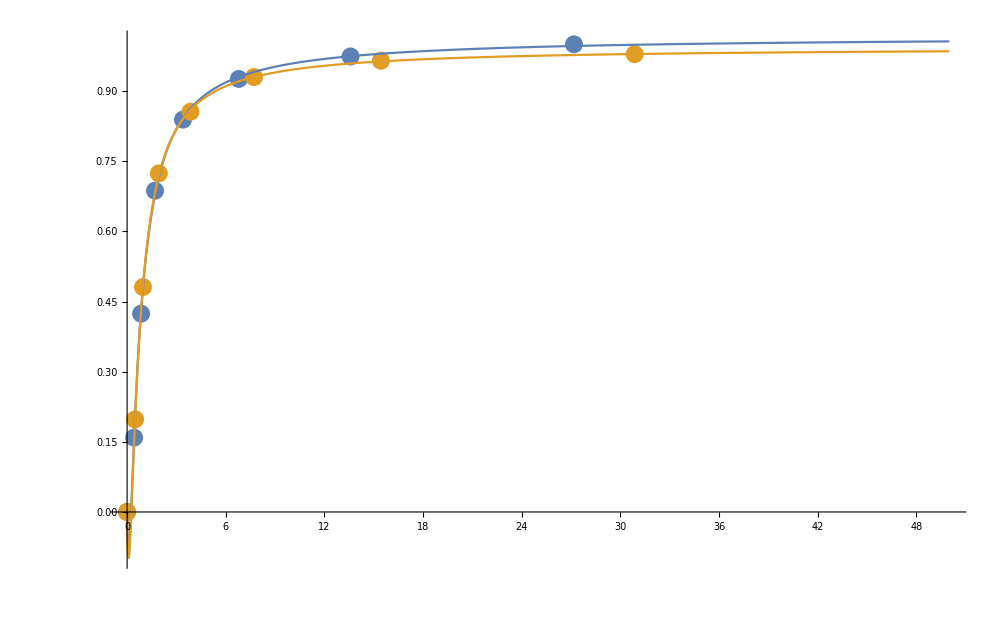

```mathematica
(*transverse*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*1*10^-6;
a0=1.84*10^-8;
a1=1.62*10^-8;
mobwet0={1,0.974,0.926,0.839,0.687,0.424,0.159,0};
mobwet1={0.979,0.965,0.930,0.856,0.724,0.481,0.198,0};

ratio0=L/a0
ratio1=L/a1

curve0=Thread[{ratio0,mobwet0}]
curve1=Thread[{ratio1,mobwet1}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit0[x_]=fitfunc2/. FindFit[ curve0,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit1[x_]=fitfunc2/. FindFit[ curve1,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p1=ListPlot[{curve0,curve1},PlotRange->All];
p2=Plot[{fit0[x],fit1[x]},{x,0,50},PlotRange->All];
Show[p1,p2,PlotRange->All]
```

{27.1739,13.587,6.79348,3.39674,1.69837,0.849185,0.424592,0.}

{30.8642,15.4321,7.71605,3.85802,1.92901,0.964506,0.482253,0.}

{{27.1739,0.939},{13.587,0.913},{6.79348,0.83},{3.39674,0.68},{1.69837,0.442},{0.849185,0.2107},{0.424592,0.069},{0.,0}}

{{30.8642,0.95},{15.4321,0.929},{7.71605,0.858},{3.85802,0.723},{1.92901,0.492},{0.964506,0.248},{0.482253,0.0855},{0.,0}}

0.960379+8.06541/(1.60449+x)^3-6.93794/(1.60449+x)^2-0.34963/(1.60449+x)

0.966814+8.44903/(1.60949+x)^3-7.27482/(1.60949+x)^2-0.297612/(1.60949+x)

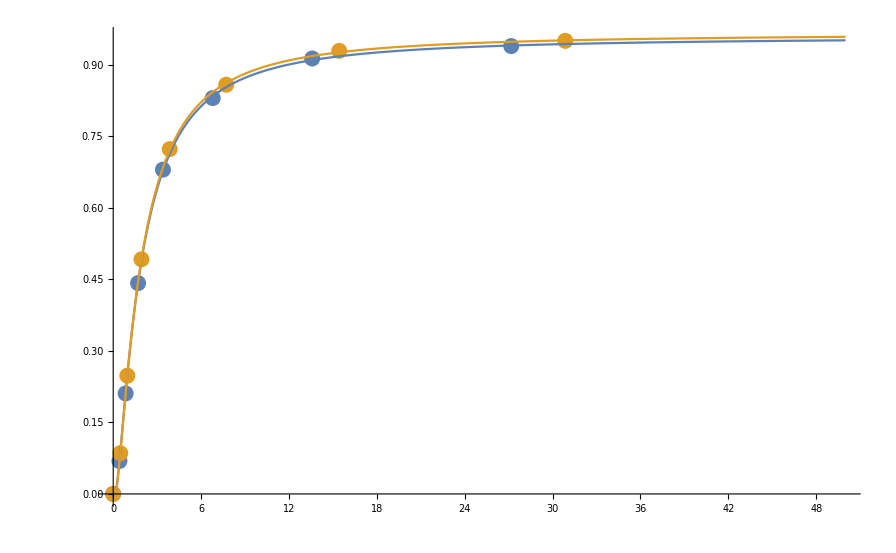

```mathematica
(*normal*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*1*10^-6;
a2=1.84*10^-8;
a3=1.62*10^-8;
mobwet2={0.939,0.913,0.830,0.680,0.442,0.2107,0.069,0};
mobwet3={0.95,0.929,0.858,0.723,0.492,0.248,0.0855,0};

ratio2=L/a2
ratio3=L/a3

curve2=Thread[{ratio2,mobwet2}]
curve3=Thread[{ratio3,mobwet3}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit2[x_]=fitfunc2/. FindFit[ curve2,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit3[x_]=fitfunc2/. FindFit[ curve3,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p3=ListPlot[{curve2,curve3},PlotRange->All];
p4=Plot[{fit2[x],fit3[x]},{x,0,50},PlotRange->All];
Show[p3,p4,PlotRange->All]
```

{12.7935,6.39674,3.19837,1.59918,0.799592,0.399796,0.199898,0.}

{14.5309,7.26543,3.63272,1.81636,0.908179,0.45409,0.227045,0.}

{{12.7935,0.9373},{6.39674,0.9063},{3.19837,0.824},{1.59918,0.6675},{0.799592,0.3967},{0.399796,0.1417},{0.199898,0.0354},{0.,0}}

{{14.5309,0.9377},{7.26543,0.9102},{3.63272,0.8418},{1.81636,0.6986},{0.908179,0.4473},{0.45409,0.1755},{0.227045,0.04453},{0.,0}}

0.937104+1.58743/(0.848985+x)^3-2.65854/(0.848985+x)^2+0.134969/(0.848985+x)

0.939334+1.45981/(0.829111+x)^3-2.46404/(0.829111+x)^2+0.0704839/(0.829111+x)

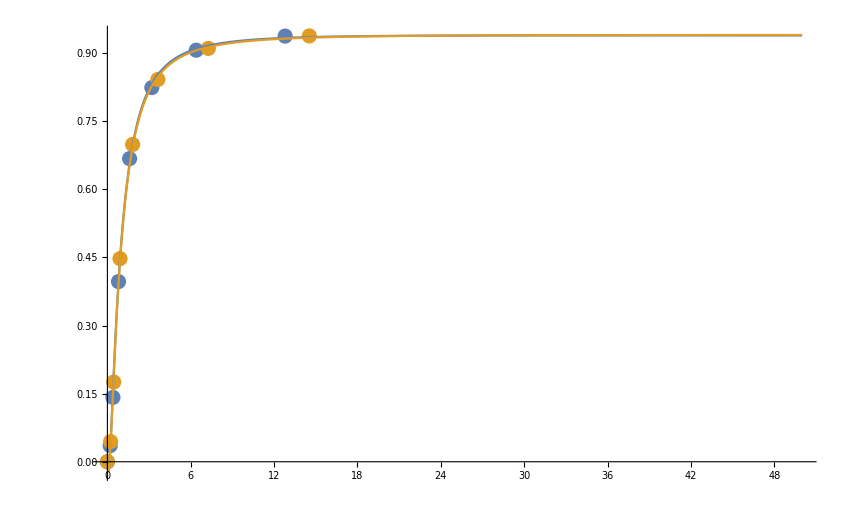

```mathematica
(*transverse*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*0.4708*10^-6;
a0=1.84*10^-8;
a1=1.62*10^-8;
mobwet0={0.9373,0.9063,0.8240,0.6675,0.3967,0.1417,0.0354,0};
mobwet1={0.9377,0.9102,0.8418,0.6986,0.4473,0.1755,0.04453,0};

ratio0=L/a0
ratio1=L/a1

curve0=Thread[{ratio0,mobwet0}]
curve1=Thread[{ratio1,mobwet1}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit0[x_]=fitfunc2/. FindFit[ curve0,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit1[x_]=fitfunc2/. FindFit[ curve1,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p1=ListPlot[{curve0,curve1},PlotRange->All];
p2=Plot[{fit0[x],fit1[x]},{x,0,50},PlotRange->All];
Show[p1,p2,PlotRange->All]
```

```mathematica
fit0[h]//FortranForm
```

0.9371039095096281 + 1.5874321625764354/(0.8489848414496414 + h)**3 - 2.658541103314216/(0.8489848414496414 + h)**2 + 
     -  0.13496873388676958/(0.8489848414496414 + h)

{12.7935,6.39674,3.19837,1.59918,0.799592,0.399796,0.199898,0.}

{14.5309,7.26543,3.63272,1.81636,0.908179,0.45409,0.227045,0.}

{{12.7935,0.8849},{6.39674,0.8219},{3.19837,0.6643},{1.59918,0.4202},{0.799592,0.1936},{0.399796,0.06193},{0.199898,0.01799},{0.,0}}

{{14.5309,0.8914},{7.26543,0.8354},{3.63272,0.689},{1.81636,0.4597},{0.908179,0.2252},{0.45409,0.07539},{0.227045,0.02213},{0.,0}}

0.878484+16.1782/(1.88467+x)^3-13.451/(1.88467+x)^2+0.928642/(1.88467+x)

0.902431+13.8063/(1.83537+x)^3-11.4215/(1.83537+x)^2+0.469594/(1.83537+x)

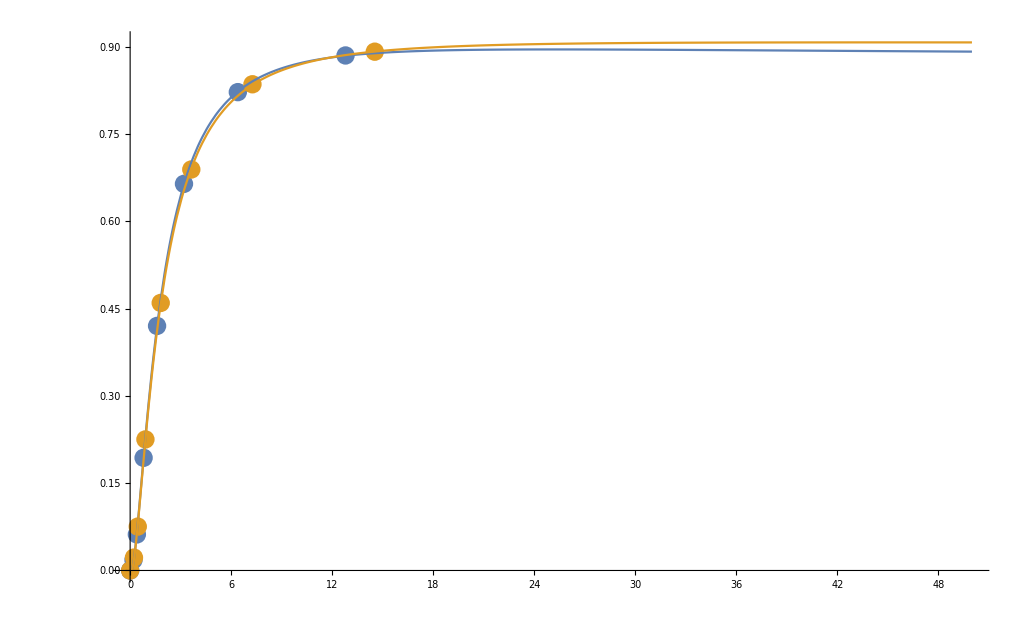

```mathematica
(*normal*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0}*0.4708*10^-6;
a2=1.84*10^-8;
a3=1.62*10^-8;
mobwet2={0.8849,0.8219,0.6643,0.4202,0.1936,0.06193,0.01799,0};
mobwet3={0.8914,0.8354,0.6890,0.4597,0.2252,0.07539,0.02213,0};

ratio2=L/a2
ratio3=L/a3

curve2=Thread[{ratio2,mobwet2}]
curve3=Thread[{ratio3,mobwet3}]
fitfunc2=aa+bb 1/(x+ff)+cc 1/(x+ff)^2+dd 1/(x+ff)^3;
fit2[x_]=fitfunc2/. FindFit[ curve2,fitfunc2,{aa,bb,cc,dd,ee,ff},x]
fit3[x_]=fitfunc2/. FindFit[ curve3,fitfunc2,{aa,bb,cc,dd,ee,ff},x]

p3=ListPlot[{curve2,curve3},PlotRange->All];
p4=Plot[{fit2[x],fit3[x]},{x,0,50},PlotRange->All];
Show[p3,p4,PlotRange->All]
```

```mathematica
fit2[h]//FortranForm
```

0.8784836695101248 + 16.178193275967942/(1.8846739602964013 + h)**3 - 13.450951287145715/(1.8846739602964013 + h)**2 + 
     -  0.9286418269991527/(1.8846739602964013 + h)